walec z=x^2/200

torus z=1/2 (x^2+y^2/21)

Dwalca = (1/100 | 0
0 | 0)

Dtorusa = (1 | 0
0 | 1/21)

obrot matrix((√3)/2 | -1/2
1/2 | (√3)/2)

DtorusRot = (16/21 | -1/(28 √3)+(√3)/4
-1/(28 √3)+(√3)/4 | 2/7)

{{1579/2100,-1/(28 √3)+(√3)/4},{-1/(28 √3)+(√3)/4,2/7}}

{-√(30/47),5 √(5/94)}

{-1,0}

szerokosc pasa obrobionego dla narzedzia poruszajacego sie wzdluz Y, wY=1.59787

{-50 √(15/74213),(√(1579/235))/2}

{0,1}

szerokosc pasa obrobionego dla narzedzia poruszajacego sie wzdluz Y, wX=2.59213

{-10 √((15 (37+20 √3))/(47 (2179+1000 √3))),(1500 √((235 (37+20 √3))/(2179+1000 √3))+1579 √((705 (37+20 √3))/(2179+1000 √3)))/(470 (6+5 √3))}

{-1/(√2),1/(√2)}

szerokosc pasa obrobionego dla narzedzia poruszajacego sie kata 45^ , w45=2.88468

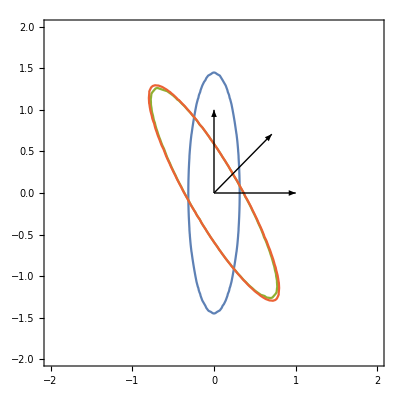

```mathematica
alfa=Pi/6;
beta=Pi/6;
Rw=100;
Rt=10;
rt=1;
T=5/100;
WalecEq[x_,y_]=1/2(1/Rw*x^2);
TorusEq[x_,y_]=1/2((1/rt)*x^2+(1/(rt+(Rt/Sin[alfa])))*y^2);
Print["walec z=", WalecEq[x,y]];
Print["torus z=", TorusEq[x,y]];
Dwalec=2*{{WalecEq[1,0],WalecEq[0,0]},{WalecEq[0,0],WalecEq[0,1]}};
Dtorus=2*{{TorusEq[1,0],TorusEq[0,0]},{TorusEq[0,0],TorusEq[0,1]}};
Print["Dwalca = ", MatrixForm[Dwalec]];
Print["Dtorusa = ", MatrixForm[Dtorus]];
Print["obrot matrix", MatrixForm[RotationMatrix[beta]]];
DtorusRot = RotationMatrix[beta].Dtorus.Transpose[RotationMatrix[beta]];
Print["DtorusRot = ", MatrixForm[DtorusRot]];
Dfz=DtorusRot-Dwalec
Zwalec=1/2*{x,y}.Dwalec.{x,y};
ZtorusRot=1/2*{x,y}.DtorusRot.{x,y};
Ztorus=1/2*{x,y}.Dtorus.{x,y};
Zfz=1/2*{x,y}.Dfz.{x,y};

(* Dla vektora = {0,1}*)
v={0,1};
w={wx,wy};
equa=Solve[{w.Dfz.w/2==T,v.Dfz.w==0},w];
(* equa has two vectors *)
w=w/.equa[[1]]
(* perpendicular to v *)
vPP={-v[[2]],v[[1]]}
wY=N[2*vPP.w];
Print["szerokosc pasa obrobionego dla narzedzia poruszajacego sie wzdluz Y, wY=", wY];

(* Dla vektora = {1,0}*)
v={1,0};
w={wx,wy};
equa=Solve[{w.Dfz.w/2==T,v.Dfz.w==0},w];
(* equa has two vectors *)
w=w/.equa[[1]]
(* perpendicular to v *)
vPP={-v[[2]],v[[1]]}
wX=N[2*vPP.w];
Print["szerokosc pasa obrobionego dla narzedzia poruszajacego sie wzdluz Y, wX=", wX];

(* Dla vektora poruszajacego sie wzdluz kata Pi/4 = {Sqrt(2)/2,Sqrt(2)/2}*)
v={Sqrt[2]/2,Sqrt[2]/2};
w={wx,wy};
equa=Solve[{w.Dfz.w/2==T,v.Dfz.w==0},w];
(* equa has two vectors *)
w=w/.equa[[1]]
(* perpendicular to v *)
vPP={-v[[2]],v[[1]]}
w45=N[2*vPP.w];
Print["szerokosc pasa obrobionego dla narzedzia poruszajacego sie kata 45^ , w45=", w45];

Show[ContourPlot[{Ztorus==T,Zwalec==T,ZtorusRot==T,ZtorusRot-Zwalec==T},{x,-2,2},{y,-2,2}],Graphics[{Arrow[{{0,0},{1,0}}],Arrow[{{0,0},{0,1}}],Arrow[{{0,0},{Sqrt[2]/2,Sqrt[2]/2}}]}]]
```